# Reflection Model Design for Wall-E and Up

## Brian Smits

## Pixar Animation Studios

This document contains the basic implementation ideas behind the reflection model for Wall-E.  The overall idea is to pick a fixed set of reflection lobes that can express a wide variety of looks and then determine how to partition the incoming energy between those lobes in such a way that energy is conserved.  The partitioning takes a relatively small set of parameters to define.

## Useful Functions

Useful helper functions.  H creates the normalized half angle vector.  n is the normal, which will always be positive z.  SphVec takes theta and phi and creates a vector.  Theta of 0 is the normal direction (+z).  FrnlBlend is the approximate Fresnel function introduced by Schlick.  The version here is generalized a little bit so that the first argument is the reflectance at normal incidence angle, the second is the reflectance at  grazing angle (always 1 for standard Fresnel)

```mathematica
H[u_,v_] := Normalize[u + v] 
n := {0,0,1};
Mix[a_, b_, t_] := a  + (b-a)t
FrnlBlend[norm_,grazing_,cos_]:=Mix[norm, grazing, (1-cos)^5];
SphVec[theta_, phi_] := {Cos[phi] Sin[theta], Sin[phi]Sin[theta], Cos[theta]}
```

Graph of the Fresnel approximation function

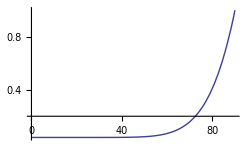

```mathematica
Plot[FrnlBlend[.04,1,Cos[(t π)/180]],{t,0,90},PlotRange->All]
```

## Diffuse

We start with the diffuse portion of the model introduced by"A Practitioners' Assessment of Light Reflection Models" Shirley et al.  It dampens the diffuse lobe for smooth surfaces when either the view or the light direction are near grazing angle to the surface by removing the reflected view or light components.  This is the BRDF lobe which will be multiplied by an N.L term later, so a traditional diffuse BRDF is a constant.  It is also missing the color term that determines how much light is absorbed inside the medium.

```mathematica
PDiffuse[u_,v_,normRefl_,grazingRefl_]:=FrnlBlend[1-normRefl,1-grazingRefl,u.n] FrnlBlend[1-normRefl,1-grazingRefl,v.n]
```

We can graph different versions of this based on different incident directions and values for the Fresnel reflectance at normal and grazing angles.  Note that if the Fresnel reflectance term at grazing angles is the same as the value at normal incident angle the diffuse term becomes a constant, exactly like traditional diffuse.  The first plot shows a dielectric at two different viewing angles. The larger curve is when viewed from 5 degrees off the surface normal, the smaller when viewed from 85 degrees off the surface normal.

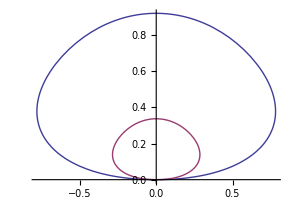

```mathematica
PolarPlot[{PDiffuse[SphVec[(5 π)/180,-π/2],SphVec[theta-π/2,π/2],0.04,1],PDiffuse[SphVec[(85 π)/180,-π/2],SphVec[theta-π/2,π/2],0.04,1]},{theta,0,π}]
```

This plot compares normal behavior with a much lower reflectance at grazing angle.  This is the behavior we want for very rough surfaces (traditional diffuse), since the FrnlBlend functions will give a constant value, so PDiffuse will be constant as well.

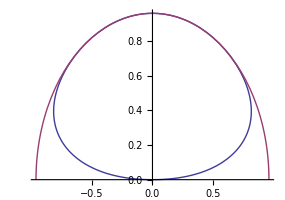

```mathematica
PolarPlot[{PDiffuse[SphVec[π/180,-π/2],SphVec[theta-π/2,π/2],0.02,1],PDiffuse[SphVec[π/180,-π/2],SphVec[theta-π/2,π/2],0.02,0.02]},{theta,0,π}]
```

And finally a 3D plot for a smooth dielectric.  The N.L term is included in the graph.

```mathematica
VP = {2.452, 1.423, 1.847}
SphericalPlot3D[PDiffuse[SphVec[(45 π)/180,-π/2],SphVec[theta,phi],0.05,1] Cos[theta],{theta,0,π/2},{phi,0,2 π},ViewPoint->VP,PlotPoints->50,PlotRange->All]
```

{2.452,1.423,1.847}

-Graphics3D-

To handle roughness for diffuse we are going to blend between this behavior and a traditional diffuse response, which means 1.  

Now we check to make sure that we aren't losing or gaining much energy.  This plot shows a graph over all incident angles and a range of grazing angle reflectance of the integral over the hemisphere, normalized by π to give a conserving energy value of 1.  Since the surface reflects at most .05 into the specular direction at normal incident angles, we should see most of the plot above about .9 or (.95 * .95).  When the surface exhibits a lot of Fresnel behavior, (roughness near 0) we should have a little less energy in the diffuse lobe, and significantly less at grazing angles.   We see that behavior below.

```mathematica
Plot3D[NIntegrate[Evaluate[(PDiffuse[Evaluate[SphVec[in* Pi / 180, 0]], Evaluate[SphVec[theta,phi]], .05 (1-rough), (1-rough)])* Cos[theta] * Sin[theta]/Pi ],{theta, 0 ,Pi/2}, {phi, 0, 2*Pi} , PrecisionGoal->4, AccuracyGoal->4], {in, 0,90}, {rough , 0, 1}, PlotRange->All]
```

-Graphics3D-

To get the diffN and diffG terms that define the diffuse response for a layer we need to look at the metallic parameter, the roughness parameter, and the surface color (surfColor). The default dielectric response is .05 (with the option to adjust this by the user, corresponding to adjusting the index of refraction of the surface), and for a metal, it is 1.  At grazing angle the default is 1 (also adjustable for various usability reasons).  Roughness blends both of these to 0.  Because of the linearity of the FrnlBlend function we can move all of the terms into the FrnlBlend term for the light once the view is fixed.  The results are checked for two different roughnesses  below

```mathematica
nRefl := Mix[.05, 1, metallic]
gRefl := 1
diffN := surfColor* Mix[(1- nRefl)FrnlBlend[1-nRefl,1-gRefl,Vdir.n], 1, rough] 
diffG := surfColor * Mix[(1- gRefl)FrnlBlend[1-nRefl,1-gRefl,Vdir.n], 1, rough]
metallic = 0;
rough = 0;
surfColor = 1;
Vdir = {0,0,1};
Ldir = {0,0,1};
FrnlBlend[diffN, diffG, Ldir.n] 
rough = 1;
FrnlBlend[diffN, diffG, Ldir.n]
```

0.9025

1.

## Specular

The specular lobe we use is based on the Distribution-based BRDF framework presented by Ashikhmin and Premoze. For the normalized distribution function we use a Gaussian of sin(theta).  Ideally, we'd like to think of the lobe as always integrating to 1, so that we can control the amount of energy going into the lobe solely by a scaling factor (the Fresnel term in the paper).  To more closely achieve this, the denominator, which tries to normalize the lobe for a given view direction when integrated over the hemisphere was also changed a bit.

The basic idea is that roughness determines an angle at which the falloff of the specular lobe drops to 10 percent. That angle and the Gaussian (of sin theta) distribution can be used to solve for an exponent.  The weight to give a normalized distribution has a very nice closed form expression, however as it turns out, the power and the weight are so close for all useful exponents that it almost doesn't matter.  Cone angle for this example goes from 5 degrees to 35 degrees based on roughness.  This is completely empirically determined and gives a broad specular highlight with very little definition.  The last expression checks that this distribution truly integrates to 1 for all values of powerS[r].

```mathematica
powerS[r_]:=-Log[0.1]/Sin[1/180 (30 r+5) π]^2
 weightS[r_]:=powerS[r]/(1-ⅇ^(-powerS[r]))
PSpecDist[ndH_,r_]:=ⅇ^(-(1-ndH^2) powerS[r]) weightS[r]
Simplify[(a TrigToExp[∫_0^(2 π) ∫_0^(π/2) ⅇ^(-(1-Cos[theta]^2) a) Cos[theta] Sin[theta]ⅆthetaⅆphi])/((1-ⅇ^-a) π)]
```

1

Here is the full specular lobe with a Fresnel weight applied.  The graph is for different roughness values for a metal with a reflectivity of .85 at some wavelength.

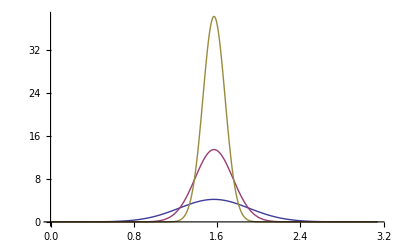

```mathematica
PSpecular[u_,v_,r_,specNormal_,specGrazing_]:=(PSpecDist[n.H[u,v],r] FrnlBlend[specNormal,specGrazing,u.H[u,v]])/((n.u^2+n.v^2-n.u n.v) 4)

Plot[{PSpecular[SphVec[(0 π)/180,-π/2],SphVec[theta-π/2,π/2],0.5,0.85,1],PSpecular[SphVec[(0 π)/180,-π/2],SphVec[theta-π/2,π/2],0.2,0.85,1],PSpecular[SphVec[(0 π)/180,-π/2],SphVec[theta-π/2,π/2],0.05,0.85,1]},{theta,0,π},PlotRange->All]
```

Here are some graphs of the lobe for a roughness of .1 for metal at different viewing angles and a dielectric at different viewing angles

```mathematica
SphericalPlot3D[PSpecular[SphVec[(85 π)/180,-π/2],SphVec[theta,phi],0.1,0.05,1] Cos[theta],{theta,0,π/2},{phi,0,2 π},ViewPoint->VP,PlotPoints->50,PlotRange->All]SphericalPlot3D[PSpecular[SphVec[(30 π)/180,-π/2],SphVec[theta,phi],0.1,0.05,1] Cos[theta],{theta,0,π/2},{phi,0,2 π},ViewPoint->VP,PlotPoints->50,PlotRange->All]
SphericalPlot3D[PSpecular[SphVec[(85 π)/180,-π/2],SphVec[theta,phi],0.1,0.85,1] Cos[theta],{theta,0,π/2},{phi,0,2 π},ViewPoint->VP,PlotPoints->50,PlotRange->All] SphericalPlot3D[PSpecular[SphVec[(30 π)/180,-π/2],SphVec[theta,phi],0.1,0.85,1] Cos[theta],{theta,0,π/2},{phi,0,2 π},ViewPoint->VP,PlotPoints->50,PlotRange->All]
```

-Graphics3D- -Graphics3D-

-Graphics3D- -Graphics3D-

Here is a function that can compute the power for a reflection lobe with a tighter cone angle.  The resulting weight would get used in a reflection version of the PSpecular function defined above.  Here the reflection cone angle goes between 0 (or epsilon in practice) and 10 degrees, however the visible range will be more in the 0 to 3 or 4 degrees range as reflection will be decreased with roughness.

```mathematica
powerR[r_]:=-Log[0.1]/Sin[1/180 (10 r) π]^2
```

This gives us two functions, PSpecular, and  a PReflection, that define two highlight lobes.  As long as we partition the normal and grazing weights passed in to these functions so that they sum to less than 1 we will conserve energy.   We distribute the energy between the two lobes based on roughness, so that at roughness 0 we have a weight of 1 on reflection and a weight of 0 on specular and the tightest reflection cone we can effectively use.  The specular cone starts out wider and grows faster, but it has a weight of 0 so it isn't seen.  As roughness increases the reflection lobe widens and the weight decreases(reflections blur and fade away) both due to the blend between specular and reflection and because of a (1-rough) term that causes the surface to become completely diffuse at roughness 1, the broader highlight from the specular also widens, and first the specular weight increases because of the blending function and eventually the (1-rough) term causes even the specular to fade away.  For efficiency reasons we have reflection fade to 0 at an intermediate roughness value so that we do not need to compute expensive reflections.  Specular is only computed directly from lights and needs to be present even for very rough surfaces so that lighters could get a rim lighting effect.  The resulting weights are fed into the PSpecular and PReflection functions.

```mathematica
reflRatio := Max[(1 - 2 *rough)^3, 0]
nRefl:=  Mix[.05, surfColor, metallic]
gRefl := 1;
specN := (1-reflRatio) *nRefl  *(1-rough)
specG := (1-reflRatio) * gRefl *(1- rough)
reflN := reflRatio  * nRefl * (1- rough)
reflG := reflRatio  * gRefl * (1 - rough)
```

## Transmission

For transmission we are taking energy that would have ended up in diffuse (due to the Fresnel weights) and instead distributing it into either transmitted diffuse, transmitted specular, or refraction.  Each of these three lobes has a form exactly like its front side equivalent.  Transmission was meant to be used mostly on either thin film objects, or objects where a highly accurate energy transfer wasn't necessary.  It was not designed for accurate rendering of glass objects.  The view direction was refracted through the surface based on the index of refraction to get a refraction direction.  That was then reflected off the surface to get a view direction on the back side of the surface that would put the center of the highlight in the correct refracted direction.   No attempt was made to change cone angles based on index of refraction, or even deal correctly with total internal reflection.  Those concessions were acceptable at that time.

Two parameters drive transmission. The first of these, clear, determines what fraction of the light that enters the surface (based on the Fresnel weights) passes straight through the surface, affected only by the surface color.  This is a description of how much scattering happens inside the material, as opposed to the scattering that happens at the interface due to roughness.  A non-transparent material would have a clear value of 0, as all light that enters the surface is scattered.  All scattered light is diffuse.    The second parameter, back, is a description of whether the scattered light (diffuse) passes through the surface and exits the opposite side, or if it exits on the side the light shines on.  A non-transparent material would have a back value of 0 saying that all light that enters the material from the front and isn't attenuated by the surface color exits from the front.

We can now rewrite the expressions for the front side weights and add in expressions for the back side using these additional two terms.  While the expressions get messier, we are still just blending between sets of energy conserving behaviors.

First the diffuse terms:

```mathematica
clear = .25;
back = .5;
nRefl := Mix[.05, 1, metallic]
gRefl := 1
dN := Mix[(1-clear)(1- nRefl)FrnlBlend[1-nRefl,1-gRefl,Vdir.n], 1 rough] 
dG := Mix[(1-clear)(1- gRefl)FrnlBlend[1-nRefl,1-gRefl,Vdir.n], 1, rough]
diffN := surfColor * dN  *(1 - back)
diffG := surfColor * dG  *(1 - back)
diffTN := surfColor * dN * back
diffTG := surfColor * dG * back
```

Now the specular and reflection terms.  Transparent metals tend not to make much sense, but there is no easy way to kill the behavior when metallic is an intermediate value.  The two color terms tend to minimize any transmission. As in the diffuse terms, there is a 1-sG term which is often 0, but if you include the ability to adjust Fresnel behavior at normal and grazing angles then that is not always true.  While this makes no sense on a real surface, it may make sense when a material is meant to represent an aggregate of lots of small transparent geometry.

```mathematica
reflRatio := Max[(1 - 2 *rough)^3, 0]
nRefl:=  Mix[.05, surfColor, metallic]
gRefl := 1;
specN := (1-reflRatio) *nRefl  *(1-rough)
specG := (1-reflRatio) * gRefl *(1- rough)
reflN := reflRatio  * nRefl * (1- rough)
reflG := reflRatio  * gRefl * (1 - rough)
specTN := surfColor * (1- reflRatio) *(1-nRefl)  *(1-rough)* clear
specTG := surfColor * (1- reflRatio) *(1-gRefl)  *(1-rough)* clear
reflTN := surfColor * reflRatio *(1-nRefl)  *(1-rough)* clear
reflTG := surfColor * reflRatio *(1-gRefl)  *(1-rough)* clear
```

## Additional Parameters

The twelve weights above can be modified by some additional parameters as well.   We allowed 2 scaling terms on the Fresnel behavior, a normal scaling term that affected nRefl and a grazing scaling term that affected gRefl.  For a dielectric nRefl allows getting the correct reflectivity based on index of refraction.  The grazing angle scaling term could be used to dampen down overly hot grazing angle specular that could result when a displaced or bump mapped surface filtered out to a smooth result.  Sometimes this isn't a problem, sometimes, such as for ground planes and large flat surfaces, it can be.

We also allowed two tint colors, one for specular and reflection, and one for transmitted specular and refraction.  These were meant to allow effects like iridescence by setting a color that was based on view direction as well as just allowing a cheap way to get out of problem situations.  These colors were multiplied into both weights of the lobes they affected.

Each of the 6 lobes had its own scaling term.  There were also scaling terms on the cone angle for each of the highlight lobes.  These controls were meant to be used both very late in the shading process to address  issues such as director notes saying "everything is perfect, make the reflection just a bit stronger and blurrier" as well as in lighting when the properties of a single object might need to be adjusted quickly and simply.

## Layering

Layering is simply a matter of taking two (or more) sets of lobe weights and cone angles and normals along with a layer weight for each layer and producing a single set.  As with determining the weights for the various lobes we do a lot of blending.    The weights can be computed with standard A over B compositing and then applied directly to the lobe weights.   The cone angles and normals for the lobes (two, one for all diffuse, one for all highlights) need to be computed a bit more carefully.  Here we determine the amount of  diffuse or specular energy by looking at the product of the lobe and layer weights and do an energy weighted blending for the normals and the cone angles.  This produces results that are much closer to what users expect from the combining of two layers.

The more complex layering that modifies the current layer by the transmitted light from the combined layers above it is a bit trickier.  The key is still making sure we account for all interactions in some plausible manner.  There is an obvious ordering of amount of  blurring of light from the reflected or refracted direction on the lobes, reflection/refraction blurs less than specular, which blurs less than diffuse.    We use this to define plausible behavior for all interactions between the three transmitted lobes of the top layer and all six of the lobes of the layer underneath.  A lobe that blurs less than the transmitted lobe type simply applies its weight to the incoming weight and replaces the direction (reflect back, or transmit through) but does not affect the cone angles or lobe type of the incoming light.  A lobe that blurs the same applies its weight to the incoming weight and replaces direction and we combine the cone angles using a max operation (a sum would probably make more sense but visually didn't seem to work as well).  A lobe that blurs more than the incoming lobe applies its weight to the incoming weight and replaces direction and lobe type and keeps any cone angle the same.  This means that for the reflected quantities of the underneath layer, reflection is the result of refracted light reflected back towards the top.  The specular contribution of the underneath layer is the sum of three interactions, and the diffuse contribution of that layer is the sum of five interactions.  This can be expressed perhaps more clearly in table form.

  Top (A)\Bottom (B) | Reflection B | Specular B | Diffuse B
Refraction A | Reflection out B | Specular out B | Diffuse out B
Transmitted Specular A | Specular out B | Specular out B | Diffuse out B
Transmitted Diffuse A | Diffuse out B | Diffuse out B | Diffuse out B
  
  There are nine additional interactions to get the accumulated transmission lobes that would be used on the next layer down.  The results of each layer add into the overall behavior of the surface.  A further complication is that users will also want the ability to have some of the layers have a presence or opacity other than 1, and of course we need to keep energy weights around for determining the two normals and the final resulting cone angles.  The end result is a relatively small amount of code that is best written in one sitting and takes almost as long to understand and verify as it does to write.

## Conclusions

Lots of the details in this model are based on an ever changing set of user requirements.  The choice of lobe for the highlights for example is easily changed as long as the new lobe also integrates to one or less over all incident angles.  The mapping from roughness to cone angle and the transitions of weights as roughness changes must make the people who will use it happy.  The exact specification of behavior at roughness 1 is also arbitrary, and the layering approaches could be made either simpler or more complicated and still work fine for partitioning energy.   Many of the decisions presented made more sense in 2006 on a film taking the first steps away from a completely non-physical model than they would in a culture already used to physically based shading.  For example, separating specular and reflection probably doesn't make sense at the interface level any more.  Internally, the separation may help when layering surfaces with broad highlights and surfaces with sharp highlights.  If more separation is needed in these cases it might even be beneficial to keep separate normals for each of the highlight lobes.

The key benefits are a fixed scattering model with a fixed amount of data required to drive it, and an approach to layering that gives the users predictable and plausible results.  With this we can map the model quite easily onto graphics hardware as well as make the lighting kernel inside of RenderMan shaders as efficient as possible.   This is true for older lighting kernels as well as newer Monte Carlo based lighting kernels.  For the users, the ability to get a wide range of appearances with a few parameters is very beneficial.  It is also helpful to have the core parameters be independent in the sense that adjusting one doesn't require a counteracting adjustment to another in order to maintain a plausible or energy conserving material.